```mathematica
Coeff[κ_,x0_]:=(√π Gamma[-1/2+κ])/(2 Gamma[κ])+Hypergeometric2F1[1/2,κ,3/2,-x0^2] x0^2
```

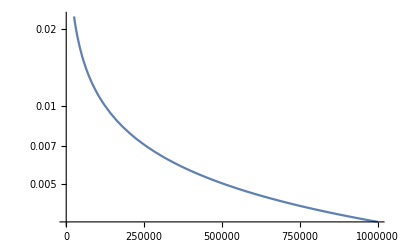

```mathematica
LogPlot[Coeff[x,3],{x,1,1000000}]
```

```mathematica
Integrate[(1+x^2)^(-κ),{x,-Infinity,Infinity},Assumptions->{κ≥ 3/2,Subscript[x, 0]≥ 0}]
```

(√π Gamma[-1/2+κ])/Gamma[κ]

```mathematica
%/.κ->3
```

(3 π)/8